## Chapter 1:

### Solved Examples

#### Ex 1.1

-Graphics-

```mathematica
A={1,-4,8};
directionCosines=ArcCos[A/Norm[A]]*180/π//N;
sumDirectioncos=Total[directionCosines]
```

227.274

#### Ex1.2

-Graphics-

```mathematica
A={1,6,18};
B={42,-69,98};
θ=ArcCos[(A.B)/(Norm[A]*Norm[B])]*180/π//N
Ba=B.(A/Norm[A])//N
Ab=(A.B)/Norm[B]//N
```

54.7689

73.2632

10.9606

#### Ex1.3

-Graphics-

```mathematica
A={-3,7,9};
B={6,-5,8};
Dvector=A×B;
Cvector=Dvector×A;
Cunitvector=Cvector/Norm[Cvector]//N
```

{0.579385,-0.538418,0.611898}

#### Ex1.4

-Graphics-

```mathematica
f=e×(d×(a×(b×c)))//Simplify
```

0.2×(d×(1×(b×c)))

#### Ex1.5

-Graphics-

```mathematica
r[t_]={8*t^2+7*t+6,5*t^3+4,0.3*t^4+2*t^2+1};
(* magnitude of the derivatives *)
v[t_]=r'[t];
MagV[t_]=Norm[v[t]];
MagV[10]
(* derivative of the magnitude *)
Magr[t_]=Sqrt[(r[t][[1]]^2+r[t][[2]]^2+r[t][[3]]^2)];
Magv1=Magr'[t]/.t->10
```

1953.33

1935.48

#### Ex1.6

-Graphics-

```mathematica
r={250,630,430};
v={90,125,170};
a={16,125,30};
ut=v/Norm[v];
ub=(v×a)/Norm[v×a];
un=ub×ut;
an=a.un//N;
ρ=Norm[v]^2/an;
centreofcurv=r+ρ*un
```

{95.1589,1141.39,135.952}

#### Ex1.7

-Graphics-

{{x[t]→x0+t V0 Cos[θ],y[t]→-4.905 t^2+y0+t V0 Sin[θ]}}

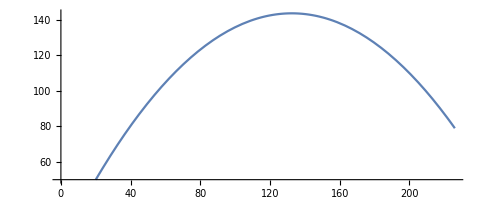

```mathematica
ClearAll[θ,x,y,g,x0,y0,V0]
g=9.81;
Sol=DSolve[{x''[t]==0,y''[t]==-g,x[0]==x0,x'[0]==V0*Cos[θ],y[0]==y0,y'[0]==V0*Sin[θ]}
      ,{x[t],y[t]},t]
x0=20;
y0=50;
V0=50;
θ=59 Degree;
ParametricPlot[{x[t],y[t]}/.Sol,{t,0,8}]
```

#### Ex1.10

-Graphics-

```mathematica
(* at state 1  we will calculate angular momentum*)
ClearAll[v0,c,d,H1,m,vx,vy,V]
v1={-v0,0,0};
r1={c,d,0};
H1=r1×(m v1);
(*at state 2 we will calculate angular momentum  *)
v2={vx,vy,0};
r2={-√(l^2-d^2),d,0};
H2=r2×(m v2);
(* we know that consevation of momentum is valid here  *)
(* we also know that n velocity component in direction of string because string is taut  *)
(*so  r2.v2=0 *)
sol=Flatten[Solve[{r2.v2==0,H1==H2},{vx,vy}]]
V=Sqrt[(vx/.sol)^2+(vy/.sol)^2]//Simplify;
Favg=m/dt Norm[({vx/.sol,vy/.sol,0}-v1)]//Simplify
```

{vx→-(d^2 v0)/l^2,vy→-(d √(-d^2+l^2) v0)/l^2}

(m √(Abs[(d √(-d^2+l^2) v0)/l^2]^2+Abs[v0-(d^2 v0)/l^2]^2))/dt

#### Ex1.13

-Graphics-
-Graphics-

```mathematica
(* problem data *)
ClearAll[r0,v0,a0,Ω,Ωd,i,j,k,Ii,Jj,Kk,r,v,a]
r0={100,200,300};
v0={-50,30,-10};
a0={-15,40,25};
Ω={1,-.4,0.6};
Ωd={-1,0.3,-.4};
i={0.557,.7428,.3714};
j={-.06331,0.4839,-0.8728};
k={-.828,0.4627,0.3166};
r={300,-100,150};
v={70,25,-20};
a={7.5,-8.5,6};
(* solution  *)
tras=Inverse[{i,j,k}];
(*  r=rel+r0 *)
rrel=r-r0
(* v=v0+Ω×rel+vrel *)
vrel=v-v0-Ω×rrel
(* a=a0+Ωd×rrel+Ω×(Ω×rrel)+2Ω×vrel *)
arel=a-a0-Ωd×rrel-Ω×(Ω×rrel)-2Ω×vrel
Arel=rrel.tras
Vrel=vrel.tras
Arel=arel.tras
```

{200,-300,-150}

{-120.,-275.,210.}

{99.5,381.5,21.}

{-167.131,-26.9127,-351.918}

{-193.125,-308.776,38.6207}

{346.609,159.982,100.764}

#### Ex1.14

-Graphics-

```mathematica
ClearAll[m,ϕ,h,v,F]
m=70000;
ϕ=30 Degree;
h=10000;
v=300;
RE=6378*1000;
Ω=2π/(23.93*3600);
a={2*Ω*(0-v*Sin[ϕ]),Ω*Sin[ϕ]*(Ω*(h+RE)*Cos[ϕ]),-v^2/(RE+h)-Ω*Cos[ϕ]*(Ω*(RE+h)*Cos[ϕ])}
F=m a
```

{-0.0218804,0.0147141,-0.0395746}

{-1531.63,1029.99,-2770.22}

#### Ex1.16

-Graphics-

```mathematica
ClearAll[h,p,n]
out=0;
taylor[n_]:=For[i=0,i≤n,i++,Print[out=out+h^i/(i!) D[Sin[t],{t,i}]]]
taylor[6]
```

Sin[t]

h Cos[t]+Sin[t]

h Cos[t]+Sin[t]-1/2 h^2 Sin[t]

h Cos[t]-1/6 h^3 Cos[t]+Sin[t]-1/2 h^2 Sin[t]

h Cos[t]-1/6 h^3 Cos[t]+Sin[t]-1/2 h^2 Sin[t]+1/24 h^4 Sin[t]

h Cos[t]-1/6 h^3 Cos[t]+1/120 h^5 Cos[t]+Sin[t]-1/2 h^2 Sin[t]+1/24 h^4 Sin[t]

h Cos[t]-1/6 h^3 Cos[t]+1/120 h^5 Cos[t]+Sin[t]-1/2 h^2 Sin[t]+1/24 h^4 Sin[t]-1/720 h^6 Sin[t]

#### Ex1.17

-Graphics-

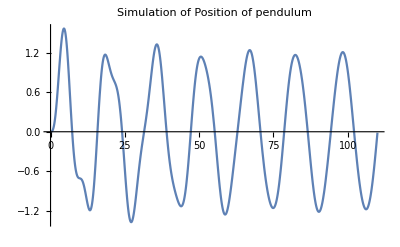

```mathematica
(*We will begin with analytical solution of mass spring system *)
t0=0;tf=110;
m=1;
ωn=1;  ζ=0.03;
F0=1;
ω=0.4;
(*Initial condition of mass spring system *)
(*x[0]==0      ,x'[0]==0*)
x0=0;
v0=0;
(*---------------------------------------*)
ωd=√(1-ζ^2) ωn;
A=(F0 ω ((2 ζ^2-1) ωn^2+ω^2))/(m ωd ((2 ζ ω ωn)^2+(ωn^2-ω^2)^2))+v0/ωd+(ζ x0 ωn)/ωd;
B=(2 ζ F0 ω ωn)/(m ((2 ζ ω ωn)^2+(ωn^2-ω^2)^2))+x0;
x[t_]=ⅇ^(-ζ t ωn) (A Sin[t ωd]+B Cos[t ωd])+(F0/(m ((2 ζ ω ωn)^2+(ωn^2-ω^2)^2))) ((ωn^2-ω^2) Sin[t ω]-2 ζ ω ωn Cos[t ω]);
Plot[x[t],{t,t0,tf},PlotLabel->"Simulation of Position of pendulum",
LabelStyle->Directive[Thick,Red]]
```

### Exercise Problems

#### Problem1

-Graphics-

```mathematica
ClearAll[A,B,Cc];
A={Ax,Ay,Az};
B={Bx,By,Bz};
Cc={Ccx,Ccy,Ccz};
Dd={Ddx,Ddy,Ddz};
A.A==(√(A[[1]]^2+A[[2]]^2+A[[3]]^2))^2
Expand[A.(B×Cc)]==Expand[(A×B).Cc]
Expand[A×(B×Cc)]==Expand[B(A.Cc)-Cc(A.B)]
```

True

True

True

#### Problem2

-Graphics-

```mathematica
Expand[(A×B).(Cc×Dd)]==Expand[(A.Cc)(B.Dd)-(A.Dd)(B.Cc)]
```

True

#### Problem3

-Graphics-

```mathematica
ClearAll[A,B,Cc,un];
A={8,9,12};
B={9,6,1};
Cc={3,5,10};
(* Get Normal component  *)
un=(A×B)/Norm[A×B];
Cn=Cc.un;
Cab=√(Norm[Cc]^2-Norm[Cn]^2)//N
```

11.5748

#### Problem4*

-Graphics-

#### Problem5

-Graphics-

```mathematica
ClearAll[V,v,ut,Vcosangles,a,ub,un,Acosangles,at,an,ρ,CC]
P[t_]={Sin[3t],Cos[t],Sin[2t]};
V[t_]=P'[t];
a[t_]=V'[t];
t0=3;
(* calculations at t=3 secs *)
V[t0]//N
v=Norm[V[t0]]//N
ut=V[t0]/v
Vcosangles=ArcCos[ut]*180/π
a[t0]//N
(* unit binormal vector ub *)
ub=(V[t]×a[t])/Norm[V[t]×a[t]]/.t->t0 //N
un=ub×ut
Acosangles=ArcCos[a[t0]/Norm[a[t0]]]*180/π//N
an=a[t0].un
at=Norm[a[t0]-an un]
ρ=v^2/an
CC=P[t0]+ρ un
```

{-2.73339,-0.14112,1.92034}

3.34351

{-0.817522,-0.0422072,0.574349}

{144.837,92.419,54.9459}

{-3.70907,0.989992,1.11766}

{-0.368509,-0.728064,-0.578035}

{-0.44256,0.684209,-0.579654}

{158.073,75.6643,73.7676}

1.67099

3.63239

6.69008

{-2.54864,3.58742,-4.15735}

#### Problem6

-Graphics-

```mathematica
ClearAll[Mman,Mwoman,r,F]
Mman=80;
Mwoman=50;
r=0.5;
G=6.6742*10^-11;             (*Universal Gravitational Constant*)
F=(G Mman Mwoman)/r^3
```

2.13574×10^-6

#### Problem7

-Graphics-

```mathematica
(* w1=(G M m)/r1^2 at the surface of the earth ,w2=(G M m)/r2^2 at distance equal to moon orbit*)
r1=6378;
r2=384.4*10^3;
W2=(r1/r2)^2 W1
```

0.000275298 W1

#### Problem8

-Graphics-

```mathematica
(*W2=(M2/M1)(r1/r2)^2 W1  where state 1 is at earth*)
Wmoon=((73.48*10^21)/(5.974*10^24))(6378/1737)^2 W1 
Wmars=((641.9*10^21)/(5.974*10^24))(6378/3396)^2 W1 
Wjupiter=((1.889*10^27)/(5.974*10^24))(6378/71490)^2 W1
```

0.165834 W1

0.378997 W1

2.51678 W1

#### Problem9

-Graphics-

```mathematica
ClearAll[G,m,M,r,v]
F1=(G M m)/r^2;
F2=(m v^2)/r;
sol=Solve[F1==F2,v];
v/.sol[[2]]
```

(√G √M)/(√r)

#### Problem10

-Graphics-

```mathematica
G=6.6742*10^-11; 
Tearth=365.25*24*3600;
rse=149.6*10^9; (* m*)
ve=2π*rse/Tearth;
me=5.974*10^24;
sol=Solve[(G Ms me)/rse^2==(me ve^2)/rse,Ms];
Ms/.sol
```

{1.9886×10^30}

#### Problem11

-Graphics-

```mathematica
ω={0,0,2};
ω'={0,0,-5};
ω''={0,0,3};
F={15,10,0};
F'''=ω''×F+2 ω'×(ω×F)+ω×(ω'×F)+ω×(ω×(ω×F))
```

{500,225,0}

#### Problem12

-Graphics-

```mathematica
(* problem data *)
ClearAll[r0,v0,a0,Ω,Ωd,i,j,k,Ii,Jj,Kk,r,v,a]
r0={-16,84,59};
v0={7,9,4};
a0={3,-7,4};
Ω={-.8,0.7,0.4};
Ωd={-0.4,0.9,-1};
i={-0.15617,-.31235,.93704};
j={-.1294,0.94698,0.29409};
k={-.97922,-0.075324,-.18831};
r={51,-45,36};
vrel={31,-68,-77};(* relative frame of reference  *)
arel={2,-6,5}; (* relative frame of reference  *)
(* solution  *)
tras={i,j,k};
(*  r=rel+r0 *)
rrel=r-r0
(* v=v0+Ω×rel+vrel *)
V=vrel.tras+v0+Ω×rrel
Vabs=Norm[V]
(* a=a0+Ωd×rrel+Ω×(Ω×rrel)+2Ω×vrel *)
A=arel.tras+a0+Ωd×rrel+Ω×(Ω×rrel)+2Ω×(vrel.tras)
Norm[A]
```

{67,-129,-23}

{121.858,-50.8775,83.85}

156.425

{-27.49,70.5231,-38.959}

85.1294

#### Problem13

-Graphics-

```mathematica
Clear[θ,i,j,k,trans,V,v,h,Ω,Vrel,vrel,Arel,A,arel]
θ'=.
i={Sin[θ],Cos[θ],0};
j={-Cos[θ],Sin[θ],0};
k={0,0,1};
trans={i,j,k};
(* velocity analysis *)
V={v,0,0};  (* Abslute velocity of the airplane  *)
rrel={h/Cos[θ],0,0}.trans;
Ω={0,0,-θ'};
Vrel={vrel,0,0}.trans
sol=Solve[V==(Vrel+Ω×rrel),{vrel,θ'}]//Simplify
(* Acceleration analysis *)
θ'=θ'/.sol;
vrel=vrel/.sol;
Ω'={0,0,-θ''};
A={0,0,0};
Arel={arel,0,0}.trans;
Ω=Flatten[Ω];
Vrel=Flatten[Vrel];
Solve[A==Arel+{0,0,-θ''}×rrel+Ω×(Ω×rrel)+2 Ω×Vrel,{arel,θ''}]//Simplify
```

{vrel Sin[θ],vrel Cos[θ],0}

{{vrel→v Sin[θ],θ'→(v Cos[θ]^2)/h}}

{{arel→(v^2 Cos[θ]^3)/h,θ''→-(2 v^2 Cos[θ]^3 Sin[θ])/h^2}}

#### Problem14

-Graphics-

```mathematica
ClearAll[m,ϕ,h,v,F]
m=1000;
ϕ=30 Degree;
h=0;
v=100*5/18;
RE=6378*1000;
Ω=2π/(23.93*3600);
a={2*Ω*(0-v*Sin[ϕ]),Ω*Sin[ϕ]*(Ω*(h+RE)*Cos[ϕ]),-v^2/(RE+h)-Ω*Cos[ϕ]*(Ω*(RE+h)*Cos[ϕ])}
F=m a
```

{-0.00202597,0.0146911,-0.0255667}

{-2.02597,14.6911,-25.5667}

#### Problem15

-Graphics-

```mathematica
ClearAll[ϕ,h,F]
ϕ=29 Degree;
g=9.81;
h=30;
RE=6378*1000;
Ω=2π/(23.93*3600);
a={0,Ω*Sin[ϕ]*(Ω*(h+RE)*Cos[ϕ]),-g};
shift=h*a[[2]]/a[[3]]
```

-0.0439945

#### Problem16

-Graphics-

```mathematica
DSolve[{0==X''[t]+2ζωn X'[t]+ωn^2 X[t],X'[0]==X0',X[0]==X0},X[t],t]
```

{{X[t]→(-ⅇ^(t (-ζωn-√(-1+ζωn^2))) X0 ζωn+ⅇ^(t (-ζωn+√(-1+ζωn^2))) X0 ζωn+ⅇ^(t (-ζωn-√(-1+ζωn^2))) X0 √(-1+ζωn^2)+ⅇ^(t (-ζωn+√(-1+ζωn^2))) X0 √(-1+ζωn^2)-ⅇ^(t (-ζωn-√(-1+ζωn^2))) X0'+ⅇ^(t (-ζωn+√(-1+ζωn^2))) X0')/(2 √(-1+ζωn^2))}}

#### Problem17*

-Graphics-

#### Problem18

-Graphics-

```mathematica
(* Ruge kutta procdure used to solve this problem *)
RK4[dy_,X0_,t0_,tf_,dt_]:=Module[{k1,k2,k3,k4,X,t,solution,i,j,n},
n=(tf-t0)/dt;                                                                                                                                   (* Number of devisions in the given time interval *)
solution =Table[0,{j,1,n,1},{i,1,Dimensions[X0][[1]],1}];                 (* initialization of solution matrix *)
(* put initial values in sol*)
For[i=1,i≤ Dimensions[X0][[1]],i++,
solution[[1]][[i]]=X0[[i]];];
(* Initializing Value Of X*)
X=X0;
t=t0;
(* Core of the function *)
For[i=1,i≤n-1,i++,
(* we eill compute slope at start of region   1st correction *)
k1=dy[X,t];
(* second correction at middle of the region *)
k2=dy[X+dt k1/2,t+dt/2];
(* third correction at middle of the region *)
k3=dy[X+dt k2/2,t+dt/2];
(* fourth correction at end of the region *)
k4=dy[X+dt k3,t+dt];
t=t+dt;
X=X+(k1 +2 k2 +2 k3 +k4)dt/6;

(*Assign solution at this point to solution matrix*)
For[j=1,j≤Dimensions[X0][[1]],j++,
solution[[i+1]][[j]]=X[[j]];];
];
Return[solution];
];
(* Define Our Problem  *)
dy[X_,t_]:=Flatten[({{X[[2]]}, {X[[3]]}, {X[[4]]}, {-X[[1]]-2X[[3]]}})];
X0=({{1}, {0}, {0}, {0}});
dt=0.005;
sol=RK4[dy,X0,0,20,dt];
sol[[20/dt,1]]
```

{9.5193}

#### Problem19

-Graphics-

```mathematica
(* Define Our Problem  *)
dy[X_,t_]:=Flatten[({{X[[2]]}, {X[[3]]}, {X[[4]]}, {12X[[1]]+4X[[2]]-3X[[3]]+t*Exp[2t]}})];
X0=({{0}, {0}, {0}, {1}});
dt=0.001;
sol=RK4[dy,X0,0,3,dt];
sol[[3/dt,1]]
(* Using Ndsolve *)
y[3]/.NDSolve[{y''''[t]+3y''[t]-4y'[t]-12y[t]==t*Exp[2t],y[0]==0,y'[0]==0,y''[0]==0,y'''[0]==1},y,{t,0,3}]
```

{32.733}

{32.8176}

#### Problem20

-Graphics-

```mathematica
(* Define Our Problem  *)
dy[X_,t_]:=Flatten[({{X[[2]]}, {2/t *X[[1]]-t X[[2]]}})];
X0=({{0}, {1}});
dt=0.01;
sol=RK4[dy,X0,1,4,dt];
sol[[(4-1)/dt,1]]
```

{1.28693}

#### Problem21

-Graphics-

```mathematica
(* Define Our Problem  *)
dy[X_,t_]:=Flatten[({{-1/2 X[[2]]+X[[3]]}, {1/2 X[[1]]-1/(√2)X[[3]]}, {-1/2 X[[1]]+1/(√2)X[[2]]}})];
X0=({{1}, {0}, {0}});
dt=0.1;
sol=RK4[dy,X0,0,20,dt];
sol[[20/dt,All]]//TableForm
(* Using NDSolve*)
ClearAll[x]
{x[20],y[20],z[20]}/.NDSolve[{x'[t]+0.5y[t]-z[t]==0,-0.5 x[t]+y'[t]+1/(√2)z[t]==0,0.5x[t]-1/(√2)y[t]+z'[t]==0,x[0]==1,y[0]==0,z[0]==0},{x,y,z},{t,0,20}]//Transpose//TableForm
```

6.20573
5.20778
3.56412

6.30318
5.26643
3.62172

#### Problem22

-Graphics-

```mathematica
(* Define Our Problem  *)
M=5.974*10^24;
G=6.67259*10^-11;
r0=384.4*10^6;
RE=6378000;
dy[X_,t_]:=Flatten[({{X[[2]]}, {(G M)/(r0-X[[1]])^2}})];
X0=({{0}, {0}});
tf=419103;   (* this is final time *)
dt=tf/2000;
sol=RK4[dy,X0,0,tf,dt];
(* Distance watched from earth centre*)
r0-sol[[tf/dt,1]]-RE
(* Comparing with analytical solution *)
t=√(r0/(2*9.81*RE^2))(π/4 r0+√(RE(r0-RE))+r0/2 ArcSin[(r0-2RE)/r0])
```

{5296.41}

418663.

#### Problem23

-Graphics-

```mathematica
ClearAll[t]
σ=10;
β=8/3;
ρ=28;
tf=50;
sol=NDSolve[{x'[t]==σ(y[t]-x[t]),y'[t]==x[t](ρ-z[t])-y[t],z'[t]==x[t]y[t]-β z[t],x[0]==0,y[0]==1,z[0]==0},{x,y,z},{t,0,tf}];
ParametricPlot3D[{x[t],y[t],z[t]}/.sol,{t,0,tf},PlotRange->All]
```

-Graphics3D-

## Chapter 2:

#### Problem1

-Graphics-

-Graphics-

#### Problem2

-Graphics-

-Graphics-

#### Problem3

-Graphics-

-Graphics-

#### Problem4

-Graphics-

```mathematica
me=5.974*10^24;                     (*Mass of the earth*)
Rearth=6378;                        (* Radius of the Earth*)
ms=1000;                            (*Mass of satellite*)
G=6.67259*10^-20;                   (*Universal Gravitational Constant*)
μ=G*(me+ms);                        (* Gravitational Parameter *)
tf=4*60*60;
n=100;
dt=(tf-0)/n;
dy[X_,t_]:={X[[2]],(-μ X[[1]])/Norm[X[[1]]]^3};
X0={{3207,5459,2714},{-6.532,0.7835,6.142}};
Sol=RK4[dy,X0,0,tf,dt];  (* Recall RK4 to Get Solution *)
R1=Sol[[All,1]];          (* Position Vector of Earth due to Satellite Mass *)
V1=Sol[[All,2]];          (* Velocity Vector of Earth *)
maximumaltitude=Max[Norm[R1[[#]]]&/@Range[n]]-Rearth
Time=Flatten[Position[Norm[R1[[#]]]&/@Range[n],Max[Norm[R1[[#]]]&/@Range[n]]]]*dt/3600//N
```

9686.89

{1.72}

#### Problem5

-Graphics-

```mathematica
me=5.974*10^24;                     (*Mass of the earth*)
Rearth=6378;                        (* Radius of the Earth*)
ms=1000;                            (*Mass of satellite*)
G=6.67259*10^-20;                   (*Universal Gravitational Constant*)
μ=G*(me+ms);                        (* Gravitational Parameter *)
tf=24*60*60;
n=1000;
dt=(tf-0)/n;
dy[X_,t_]:={X[[2]],(-μ X[[1]])/Norm[X[[1]]]^3};
X0={{6600,0,0},{0,12,0}};
Sol=RK4[dy,X0,0,tf,dt];  (* Recall RK4 to Get Solution *)
R1=Sol[[All,1]];          (* Position Vector of Earth due to Satellite Mass *)
V1=Sol[[All,2]];          (* Velocity Vector of Earth *)
Norm[R1[[n,All]]]
Norm[V1[[n,All]]]
```

462716.

4.99286

#### Problem6

-Graphics-

```mathematica
ClearAll[r,v]
r[t_]={t Sin[t],t^2 Cos[t],t^3 Sin[t]^2};
v[t_]=r'[t];
D[√((r[t][[1]])^2+(r[t][[2]])^2+(r[t][[3]])^2),t]/.t->2//N
Norm[v[t]]/.t->2//N
```

4.89394

6.56292

#### Problem7

-Graphics-

-Graphics-

#### Problem8

-Graphics-

-Graphics-

#### Problem9

-Graphics-

-Graphics-

#### Problem10

-Graphics-

-Graphics-

#### Problem11

-Graphics-

```mathematica
ClearAll[r,v,h,e,μ,θ]
me=5.974*10^24;                     (*Mass of the earth*)
G=6.67259*10^-20;                   (*Universal Gravitational Constant*)
μ=G*me; 
r={7000,-2000,-4000};
v={3,-6,5};
(* specific angular momentum h *)
h=r×v;
e=(v×h)/μ-r/Norm[r]
θ=ArcCos[(e.r)/(Norm[e]*Norm[r])]*180/Pi
```

{0.288701,0.0852353,-0.383941}

33.3258

#### Problem12*

-Graphics-

#### Problem13

-Graphics-

```mathematica
ClearAll[r,v,ur,ut,γ]
v={-4,3,-5};
ur={0.26726,0.53452,0.80178};
vr=v.ur
vt=√(Norm[v]^2-vr^2)
γ=ArcTan[vt,vr]*180/Pi
```

-3.47438

6.15863

-29.4295

#### Problem14

-Graphics-

-Graphics-

#### Problem15*

-Graphics-

#### Problem16

-Graphics-

```mathematica
ClearAll[r,v,h,e,μ,θ]
me=5.974*10^24;                     (*Mass of the earth*)
G=6.67259*10^-20;                   (*Universal Gravitational Constant*)
μ=G*me; 
h=60000;
r=h^2/μ;
T=(2π)/(√μ)r^(3/2)/3600
```

2.37253

#### Problem17

-Graphics-

```mathematica
me=641.9*10^21;                     (*Mass of the mars*)
G=6.67259*10^-20;                   (*Universal Gravitational Constant*)
μ=G*me; 
r=200+3396;
v=√(μ/r)
T=(2π)/(√μ)r^(3/2)/3600
```

3.45121

1.81855

#### Problem18

-Graphics-

```mathematica
ClearAll[A,a,b,T]
A/.Solve[A/(T/4)==(π a b)/T,A]//N
```

{0.785398 a b}

#### Problem19

-Graphics-

-Graphics-

#### Problem20

-Graphics-

-Graphics-

#### Problem21

-Graphics-

```mathematica
me=5.974*10^24;                     (*Mass of the earth*)
G=6.67259*10^-20;                   (*Universal Gravitational Constant*)
Rearth=6378; 
μ=G*me;
ra=100000;
rp=10000;
r=10000+Rearth;
e=(ra-rp)/(ra+rp)//N
a=(ra+rp)/2
T=(2π)/(√μ)a^(3/2)/3600
ϵ=-μ/(2a);
θ=ArcCos[1/e((a(1-e^2))/r-1)]*180/Pi
h=√(r μ(1+e Cos[θ Degree]));
vr=μ/h e Sin[θ Degree]  (* Axial component of velocity *)
vt=μ/h(1+e Cos[θ Degree])    (* vertical comoponent of velocity  *)
Vperigee=μ/h √(1+e^2+2e Cos[0])  (* speed at perigee *)
Vapogee=μ/h √(1+e^2+2e Cos[π])  (* Speed at the apogee *)
```

0.818182

55000

35.6567

82.2638

3.79612

5.19802

8.51331

0.851331

#### Problem22

-Graphics-

```mathematica
μ=398621;
Rearth=6378; 
rp=Rearth+400;
ra=Rearth+600;
a=(rp+ra)/2;
T=((2π)/μ^(1/2)a^(3/2)/2)/60//N   (* Time of half period  *)
```

47.3055

#### Problem23

-Graphics-

```mathematica
μ=398621;
Rearth=6378; 
rp=Rearth+500;
ra=Rearth+2000;
e=(ra-rp)/(ra+rp)//N
h=√(rp*μ*(1+e));
Vperigee=h/rp
Vapogee=h/ra
T=((2π)/(√μ)a^(3/2))/60//N
```

0.098322

7.97836

6.54991

94.611

#### Problem24

-Graphics-

```mathematica
ClearAll[e]
μ=398621;
Rearth=6378; 
rp=Rearth+500;
Vperigee=10;
(*  Calculations  *)
h=Vperigee*rp;
e=e/.Solve[rp==h^2/μ*1/(1+e),e]//N
γ=ArcTan[(e Sin[120 Degree])/(1+e Cos[120 Degree])]*180/π
alt=h^2/μ*1/(1+e Cos[120 Degree])-Rearth
```

{0.725448}

{44.5917}

{12244.4}

#### Problem25

-Graphics-

```mathematica
ClearAll[θ,h,e]
μ=398621;
Rearth=6378; 
r=Rearth+1000;
v=10;
γ=15 Degree;
sol=Solve[{r==h^2/μ*1/(1+e Cos[θ]),Tan[γ]==(e Sin[θ])/(1+e Cos[θ]),v==μ/h √(1+e^2+2e Cos[θ])},{θ,h,e}]//N;
θ=(θ/.sol[[1]])*180/π
h=h/.sol[[1]]
e=e/.sol[[1]]
a=h^2/(μ(1-e^2));
T=(2π)/(√μ)a^(3/2)/3600
```

32.4796

71266.

0.861677

30.4232

#### Problem26

-Graphics-

```mathematica
μ=398621;
Rearth=6378; 
rp=500+Rearth;
ra=21000+Rearth;
(* Solution *)
e=(ra-rp)/(ra+rp)//N
a=(ra+rp)/2;
T=(2π)/(√μ)a^(3/2)/3600//N
(*  Maximum speed at the perigee *)
h=√(a*μ(1-e^2));
Vmax=h/rp
```

0.598435

6.19665

9.62491

#### Problem27

-Graphics-

```mathematica
ClearAll[e]
μ=398600;
Rearth=6378; 
(* parallel to earth surface so θ=0 *)
v=7.7;  (* I here changed the input value because this number gives eccentricity less than 0 *)
rp=Rearth+500;
h=v*rp;
e=e/.Solve[{rp==h^2/μ*1/(1+e)},{e}]
a=rp/(1-e);
T=(2π)/(√μ)a^(3/2)/3600
```

{0.0230723}

{1.63308}

#### Problem28

-Graphics-

```mathematica
ClearAll[a,h,e]
μ=398600;
Rearth=6378;
v=8;
T=2*3600;
(* Problem givens is in complete so we will assume θ=0 *)
a=(a/.Solve[T==(2π)/(√μ) a^(3/2),a])//N;
sol=NSolve[{v==μ/h(1+e),a==h^2/(μ(1-e^2))},{e,h}];
h=h/.sol;
e=e/.sol;
alt=h/v-Rearth
(* out assumption is true *)
```

{648.248}

#### Problem29

-Graphics-

```mathematica
ClearAll[a]
μ=398600;
Rearth=6378;
rp=200+Rearth;
T=100*60;
(* Solution *)
a=(a/.NSolve[T==(2π)/(√μ) a^(3/2),a])//N;
e=1-rp/a
```

{0.0782768}

#### Problem30

-Graphics-

```mathematica
ClearAll[θ,e,h]
μ=398600;
Rearth=6378;
v=7.5;
γ=10 Degree;
r=8000;
(* we will solve three equations in 3 unknowns*)
sol=NSolve[{v==μ/h √(1+e^2+2e Cos[θ]),Tan[γ]==(e Sin[θ])/(1+e Cos[θ]),r==h^2/μ*1/(1+e Cos[θ])},{θ,e,h}];
θ=(θ/.sol[[2]])*180/π
e=e/.sol[[2]]
```

63.8213

0.21513

#### Problem31

-Graphics-

```mathematica
ClearAll[θ,h,e]
μ=398600;
v=7.5;
γ=10 Degree;
r=8000;
output=NSolve[{r==h^2/μ*1/(1+e Cos[θ]),v==μ/h √(1+e^2+2e Cos[θ]),Tan[γ]==(e Sin[θ])/(1+e Cos[θ])},{θ,e,h}];
θ=(θ/.output[[2]])*180/π
e=e/.output[[2]]
```

63.8213

0.21513

#### Problem32

-Graphics-

```mathematica
ClearAll[e,rp,ra]
μ=398600;
Rearth=6378;
h=70000;
ϵ=-10;
(* Solution *)
e=e/.NSolve[ϵ==-1/2*μ^2/h^2(1-e^2),e][[2]];
a=h^2/(μ(1-e^2));
sol=NSolve[{e==(ra-rp)/(ra+rp) ,a==(ra+rp)/2 },{rp,ra}]
rp=(rp/.sol)-Rearth
ra=(ra/.sol)-Rearth
```

{{rp→7592.87,ra→32267.1}}

{1214.87}

{25889.1}

#### Problem33

-Graphics-

```mathematica
ClearAll[e,θ,h]
μ=398600;
Rearth=6378;
v=7;
r=1000+Rearth;
γ=10 Degree ;
(* we will solve three equations in 3 unknowns*)
sol=NSolve[{v==μ/h √(1+e^2+2e Cos[θ]),Tan[γ]==(e Sin[θ])/(1+e Cos[θ]),r==h^2/μ*1/(1+e Cos[θ])},{θ,e,h}];
e=e/.sol[[2]];
h=h/.sol[[2]];
a=h^2/(μ(1-e^2));
T=(2π)/(√μ)a^(3/2)/60
```

91.9868

#### Problem34

-Graphics-

-Graphics-

#### Problem35

-Graphics-

-Graphics-

#### Problem36

-Graphics-

```mathematica
μ=398600;
Rearth=6378;
vesc=√((2μ)/Rearth)//N
```

11.18

#### Problem37

-Graphics-

```mathematica
ClearAll[e]
μ=398600;
Rearth=6378;
rp=Rearth+250;
vp=11;
(* hyperpolic excess speed *)
h=rp*vp;
e=e/.NSolve[rp==h^2/μ*1/(1+e Cos[0]),e];
Subscript[v, ∞]=μ/h √(e^2-1)
r=h^2/μ*1/(1+e Cos[100 Degree])
Subscript[v, r]=μ/h e Sin[100 Degree]
Subscript[v, t]=μ/h(1+e Cos[θ])
```

{0.849935}

{16178.8}

{5.44878}

{(99650 (1+1.01201 Cos[θ]))/18227}

#### Problem38

-Graphics-

```mathematica
ClearAll[e,h]
μ=398600;
Rearth=6378;
r=402000;
θ=150 Degree;
v=2.23;
output=NSolve[{r==h^2/μ*1/(1+e Cos[θ]),v==μ/h √(1+e^2+2e Cos[θ])},{e,h}];
e=e/.output[[2]]
h=h/.output[[2]];
hp=-Rearth+h^2/μ*1/(1+e Cos[0])
vp=h/(hp+Rearth)
```

1.086

5087.59

8.51585

#### Problem39

-Graphics-

-Graphics-

#### Problem40

-Graphics-

-Graphics-

#### Problem41

-Graphics-

```mathematica
ClearAll[θ,h,e]
μ=398600;
v=10;
r=10000;
γ=(120-90) Degree;
output=NSolve[{r==h^2/μ*1/(1+e Cos[θ]),v==μ/h √(1+e^2+2e Cos[θ]),Tan[γ]==(e Sin[θ])/(1+e Cos[θ])},{θ,e,h}];
θ=(θ/.output[[2]])*180/π
```

50.9399

#### Problem42

-Graphics-

-Graphics-

#### Problem43

-Graphics-

-Graphics-

#### Problem44

-Graphics-

```mathematica
(* Lagrangian coefficient implementation  *)
LagrangeCoefficients[μ_,r0_,v0_,θ_]:=Module[{Magr0,Magv0,Magvr0,h,Magr,f,g,fdot,gdot,LC,r,v},
(* Magnitude of r0*)
Magr0=√(r0.r0);
(* Magnitude of v0*)
Magv0=√(v0.v0);
(* Magnitude of Axial component of velocity vr0*)
Magvr0=(r0.v0)/Magr0;
(* Magnitude of specific angular momentum *)
h=Magr0*√(Magv0^2-Magvr0^2);
(* Magnitude of r*)
Magr=h^2/μ*1/(1+(h^2/(μ*Magr0)-1)*Cos[θ]-(h*Magvr0)/μ*Sin[θ]);
(* Lagrangian coeeficints and it`s derivatives *)
f=1-(μ*Magr)/h^2*(1-Cos[θ]);
g=(Magr*Magr0)/h*Sin[θ];
fdot=μ/h*(1-Cos[θ])/Sin[θ]*(μ/h^2 (1-Cos[θ])-1/Magr0-1/Magr);
gdot=1-(μ*Magr0)/h^2(1-Cos[θ]);
(* Calculate new states  *)
LC={{f,g},{fdot,gdot}};
r=LC[[1]].{r0,v0};
v=LC[[2]].{r0,v0};
(* return output *)
Return[{r,v}]//N];
(* Solution *)
ClearAll[e,θ0]
r0={7000,0,0};
v0={7,7,0};
μ=398600;
θ=90 Degree;
output=LagrangeCoefficients[μ,r0,v0,θ];
r=output[[1]]
v=output[[2]];
h0=r0×v0;
Magr0=Norm[r0];
Magv0=Norm[v0];
Magh0=Norm[h0];
output=NSolve[{Magr0==Magh0^2/μ*1/(1+e Cos[θ0]),Magv0==√(1+e^2+2e Cos[θ0])},{e,θ0}];
θ0=(θ0/.output[[4]])*180/π
```

{0.,43183.5,0.}

90.8103

#### Problem45

-Graphics-

```mathematica
(* Solution *)
r0={3450,-1700,7750};
v0={5.4,-5.4,1};
μ=398600;
θ=82 Degree;
output=LagrangeCoefficients[μ,r0,v0,θ];
r=Norm[output[[1]]]
v=Norm[output[[2]]]
(* check if r×v=r0×v0 *)
output[[1]]×output[[2]]==r0×v0
(*  energy is conserved because h is constant and e *)
```

19266.2

2.92513

True

#### Problem46

-Graphics-

```mathematica
ClearAll[g,f,r]
(* Solution *)
r0={6320,0,7750};
v0={0,11,0};
μ=398600;
Subscript[r, p]=Norm[r0];
Subscript[v, p]=Norm[v0];
(* then calculate lagrange coefficients *)
f[t_]=1-μ/(2*Subscript[r, p]^3)*t^2+μ/2*(r0.v0)/Subscript[r, p]^5*t^3+μ/24((-2μ)/Subscript[r, p]^6+(3 Subscript[v, p]^2)/Subscript[r, p]^5-15*(r0.v0)^2/Subscript[r, p]^7)*t^4//N;
g[t_]=t-1/6*μ/Subscript[r, p]^3*t^3+μ/4*(r0.v0)/Subscript[r, p]^5*t^4//N;
r[t_]:=f[t]*r0+g[t]*v0
r[10*60]
(* Comparing results with ND solve *)
T=10*60;
Subscript[R, exact][t_]=R[t]/.NDSolve[{R''[t]==(-μ*R[t])/Norm[R[t]]^3,R'[0]==v0,R[0]==r0},R,{t,0,T}];
Subscript[R, exact][T]
(* to get change in true anomaly  *)
ClearAll[e,θ1,θ2]
h0=Norm[r0×v0];
output=NSolve[{Subscript[r, p]==h0^2/μ*1/(1+e Cos[θ1]),Subscript[v, p]==μ/h0*√(1+e^2+2e Cos[θ1])},{e,θ1}];
e=e/.output[[3]];
θ1=θ1/.output[[3]];
θ2=(θ2/.Solve[Norm[Norm[Subscript[R, exact][T]]]==h0^2/μ*1/(1+e Cos[θ2]),θ2][[2]])*180/π
```

{5905.12,6442.17,7241.24}

{{5899.98,6460.7,7234.94}}

34.6851

#### Problem47

-Graphics-

#### Problem48

-Graphics-